1/2k(p[t]-v t)^2+(c1+c2 q[t]^2)(1-Cos[2Pi(p[t]-c3 q[t])/a])+c4 q[t]^4

-1. (-1. t+p[t])-2.51327×10^10 (1.3×10^-20+0.2 q[t]^2) Sin[2.51327×10^10 (p[t]-1. q[t])]

-0.4 (1.-1. Cos[2.51327×10^10 (p[t]-1. q[t])]) q[t]-3.2×10^19 q[t]^3+2.51327×10^10 (1.3×10^-20+0.2 q[t]^2) Sin[2.51327×10^10 (p[t]-1. q[t])]

{{p[t]→                                 -9
InterpolatingFunction[{{0., 5. 10  }}, <>][t],q[t]→                                 -9
InterpolatingFunction[{{0., 5. 10  }}, <>][t]}}

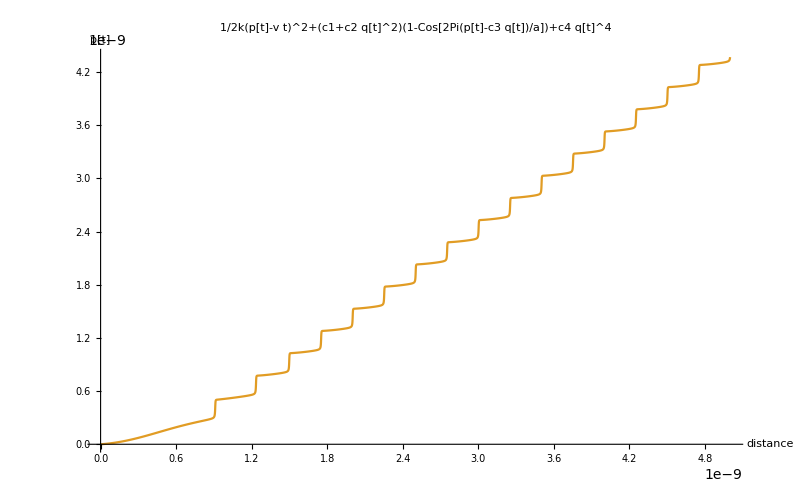

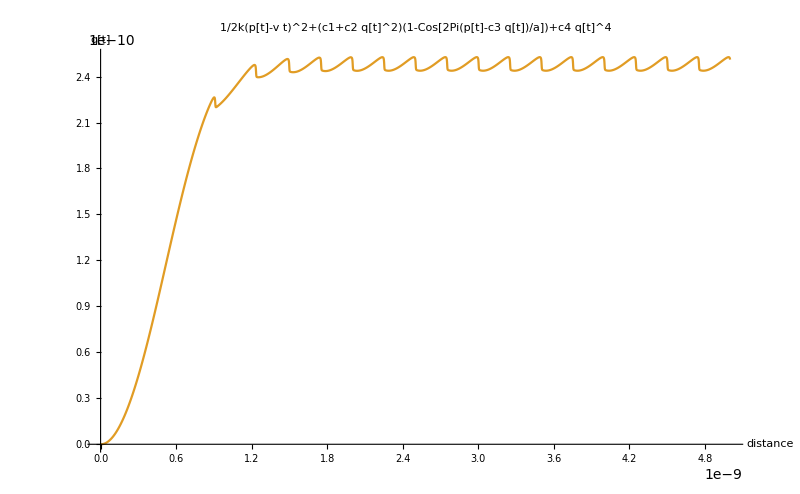

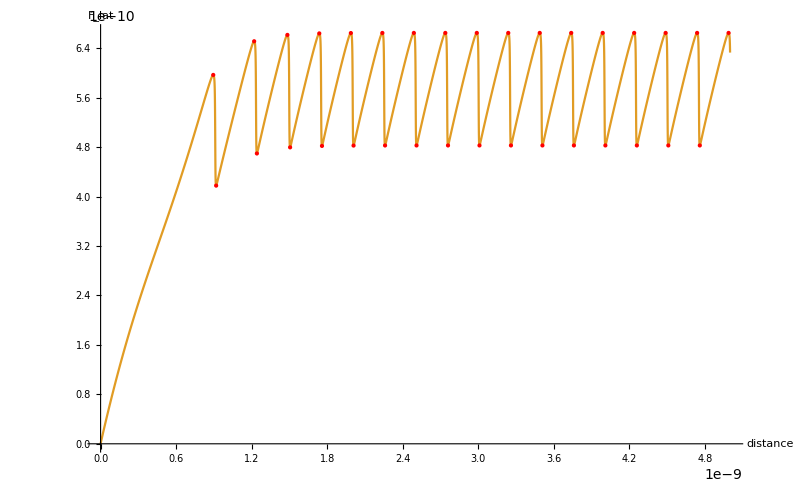
-Graphics-1/2k(p[t]-v t)^2+(c1+c2 q[t]^2)(1-Cos[2Pi(p[t]-c3 q[t])/a])+c4 q[t]^4

```mathematica
(*main program, making plots for fric, p, q*)


Needs["DifferentialEquations`NDSolveUtilities`"];

SetDirectory["/home/storluffarn/phd-stuff/research/graphene/images/"];

(*reference values*)
(*k = 1.0; (*Li: 0.8*)
v = 1; (*Li: 2*)
c1=1.3*^-20; (*Li: ~9*^-17?!*)
c2=0.2;
c3=8*^18;
c4=1;
a = 2.5*^-10; (*Li: 2.5*^-10*)
mp = 1*^-23;
mq = 5*^-22;
ηp = 3*^12;
ηq= 3*^12;
h = 1*^-15;
tmax=5000000h;*)

(*parameters*)
k = 1.0; (*Li: 0.8*)
v = 1; (*Li: 2*)
c1=1.3*^-20; (*Li: ~9*^-17?!*)
c2=0.2;
c3=8*^18;
c4=1;
a = 2.5*^-10; (*Li: 2.5*^-10*)
mp = 1*^-23;
mq = 5*^-22;
ηp = 3*^12;
ηq= 1.5*^12;
h = 1*^-15;
tmax=5000000h;

(*noise*)

s1=0.05;
s2=0.035;
s3=0.025;

phscale=4*^9;
p1=1phscale;
p2=2phscale;
p3=5phscale;
num=1;
lim=2;
terms=5;

enscale=1*^-19;
r=Table[RandomReal[{-num,num}],{t,0,100}];
ϵ[t_]:=t;(*for fucntional input*)
(*n[ϵ[t_]]:=enscale(s3 Sum[r[[2i+1]]Cos[ p3 r[[2i+1+1]] ϵ[t]],{i,0,terms-1}]+s2 Sum[r[[2i+1]]Cos[ p2 r[[2i+1+1]]ϵ[ t]],{i,terms,2terms-1}]+s1 Sum[r[[2i+1]]Cos[ p1 r[[2i+1+1]]ϵ[t]],{i,2terms,2terms-1}])*)

(*var="v";
t1=v/2;
t2=v;
t3=v*2;

varr="η_q";
t11=ηq/2;
t22=ηq;
t33=ηq*2;

varrr="c3";
t111=c4/2;
t222=c4;
t333=c4*2;

varrrr="mq";
t1111=mq/2;
t2222=mq;
t3333=mq*2;*)

(*potential, will reuse string later for headers*)
anpotstring="1/2k(p[t]-v t)^2+(c1+c2 q[t]^2)(1-Cos[2Pi(p[t]-c3 q[t])/a])+c4 q[t]^4"
anpotstringtmp="1/2k(p[t]-v t)^2+(c1+c2 q[t]^2)(1-Cos[2Pi(p[t]-c4 q[t])/a])+c3 q[t]^4";
anpot=ToExpression[anpotstringtmp];
(*anpot=1/2k(p[t]-v t)^2+V01(1-Cos[2Pi(p[t]-q[t])/a])-V02(Cos[2Pi q[t]/a]);*)
-N@D[anpot,p[t]]
-N@D[anpot,q[t]]

(*diff solver, stiffness switching is good for numerically striff stiff problems*)
s=NDSolve[{-mp p''[t]-D[anpot,p[t]]-mp ηp (p'[t])==0,-mq q''[t]-D[anpot,q[t]]-mq ηq(q'[t])==0,p[0]==0,p'[0]==0,q[0]==0,q'[0]==0},{p[t],q[t]},{t,0,tmax},MaxSteps->1000000,Method->{"StiffnessSwitching"}] (*,Method->{"StiffnessSwitching"} AccuracyGoal->∞, "TimeIntegration"-> *)

(*anpot1=1/2k(p[t]-t1 t)^2+(c1+c2 q[t]^2)(1-Cos[2Pi(p[t]-c4 q[t])/a])+c3 q[t]^4;
anpot2=1/2k(p[t]-t2 t)^2+(c1+c2 q[t]^2)(1-Cos[2Pi(p[t]-c4 q[t])/a])+c3 q[t]^4;
anpot3=1/2k(p[t]-t3 t)^2+(c1+c2 q[t]^2)(1-Cos[2Pi(p[t]-c4 q[t])/a])+c3 q[t]^4;*)
(*anpot11=1/2k(p[t]-v t)^2+(c1+c2 q[t]^2)(1-Cos[2Pi(p[t]-c4 q[t])/a])+c3 q[t]^4;
anpot22=1/2k(p[t]-v t)^2+(c1+c2 q[t]^2)(1-Cos[2Pi(p[t]-c4 q[t])/a])+c3 q[t]^4;
anpot33=1/2k(p[t]-v t)^2+(c1+c2 q[t]^2)(1-Cos[2Pi(p[t]-c4 q[t])/a])+c3 q[t]^4;
anpot111=1/2k(p[t]-v t)^2+(c1+c2 q[t]^2)(1-Cos[2Pi(p[t]-t111 q[t])/a])+c3 q[t]^4;
anpot222=1/2k(p[t]-v t)^2+(c1+c2 q[t]^2)(1-Cos[2Pi(p[t]-t222 q[t])/a])+c3 q[t]^4;
anpot333=1/2k(p[t]-v t)^2+(c1+c2 q[t]^2)(1-Cos[2Pi(p[t]-t333 q[t])/a])+c3 q[t]^4;
anpot1111=1/2k(p[t]-v t)^2+(c1+c2 q[t]^2)(1-Cos[2Pi(p[t]-c4 q[t])/a])+c3 q[t]^4;
anpot2222=1/2k(p[t]-v t)^2+(c1+c2 q[t]^2)(1-Cos[2Pi(p[t]-c4 q[t])/a])+c3 q[t]^4;
anpot3333=1/2k(p[t]-v t)^2+(c1+c2 q[t]^2)(1-Cos[2Pi(p[t]-c4 q[t])/a])+c3 q[t]^4;*)

(*s1=NDSolve[{-mp p''[t]-D[anpot1,p[t]]-mp ηp(p'[t])==0,-mq q''[t]-D[anpot1,q[t]]-mq ηq(q'[t])==0,p[0]==0,p'[0]==0,q[0]==0,q'[0]==0},{p[t],q[t]},{t,0,2tmax},MaxSteps->1000000,Method->{"StiffnessSwitching"}];
s2=NDSolve[{-mp p''[t]-D[anpot2,p[t]]-mp ηp(p'[t])==0,-mq q''[t]-D[anpot2,q[t]]-mq ηq(q'[t])==0,p[0]==0,p'[0]==0,q[0]==0,q'[0]==0},{p[t],q[t]},{t,0,tmax},MaxSteps->1000000,Method->{"StiffnessSwitching"}];
s3=NDSolve[{-mp p''[t]-D[anpot3,p[t]]-mp ηp(p'[t])==0,-mq q''[t]-D[anpot3,q[t]]-mq ηq(q'[t])==0,p[0]==0,p'[0]==0,q[0]==0,q'[0]==0},{p[t],q[t]},{t,0,tmax},MaxSteps->1000000,Method->{"StiffnessSwitching"}];*)

(*s11=NDSolve[{-mp p''[t]-D[anpot11,p[t]]-mp ηp(p'[t])==0,-mq q''[t]-D[anpot11,q[t]]-mq t11(q'[t])==0,p[0]==0,p'[0]==0,q[0]==0,q'[0]==0},{p[t],q[t]},{t,0,tmax},MaxSteps->1000000,Method->{"StiffnessSwitching"}];
s22=NDSolve[{-mp p''[t]-D[anpot22,p[t]]-mp ηp(p'[t])==0,-mq q''[t]-D[anpot22,q[t]]-mq t22(q'[t])==0,p[0]==0,p'[0]==0,q[0]==0,q'[0]==0},{p[t],q[t]},{t,0,tmax},MaxSteps->1000000,Method->{"StiffnessSwitching"}];
s33=NDSolve[{-mp p''[t]-D[anpot33,p[t]]-mp ηp(p'[t])==0,-mq q''[t]-D[anpot33,q[t]]-mq t33(q'[t])==0,p[0]==0,p'[0]==0,q[0]==0,q'[0]==0},{p[t],q[t]},{t,0,tmax},MaxSteps->1000000,Method->{"StiffnessSwitching"}];

s111=NDSolve[{-mp p''[t]-D[anpot111,p[t]]-mp ηp(p'[t])==0,-mq q''[t]-D[anpot111,q[t]]-mq ηq(q'[t])==0,p[0]==0,p'[0]==0,q[0]==0,q'[0]==0},{p[t],q[t]},{t,0,tmax},MaxSteps->1000000,Method->{"StiffnessSwitching"}];
s222=NDSolve[{-mp p''[t]-D[anpot222,p[t]]-mp ηp(p'[t])==0,-mq q''[t]-D[anpot222,q[t]]-mq ηq(q'[t])==0,p[0]==0,p'[0]==0,q[0]==0,q'[0]==0},{p[t],q[t]},{t,0,tmax},MaxSteps->1000000,Method->{"StiffnessSwitching"}];
s333=NDSolve[{-mp p''[t]-D[anpot333,p[t]]-mp ηp(p'[t])==0,-mq q''[t]-D[anpot333,q[t]]-mq ηq(q'[t])==0,p[0]==0,p'[0]==0,q[0]==0,q'[0]==0},{p[t],q[t]},{t,0,tmax},MaxSteps->1000000,Method->{"StiffnessSwitching"}];

s1111=NDSolve[{-mp p''[t]-D[anpot1111,p[t]]-mp ηp(p'[t])==0,-t1111 q''[t]-D[anpot1111,q[t]]-t1111 ηq(q'[t])==0,p[0]==0,p'[0]==0,q[0]==0,q'[0]==0},{p[t],q[t]},{t,0,tmax},MaxSteps->1000000,Method->{"StiffnessSwitching"}];
s2222=NDSolve[{-mp p''[t]-D[anpot2222,p[t]]-mp ηp(p'[t])==0,-t2222 q''[t]-D[anpot2222,q[t]]-t2222 ηq(q'[t])==0,p[0]==0,p'[0]==0,q[0]==0,q'[0]==0},{p[t],q[t]},{t,0,tmax},MaxSteps->1000000,Method->{"StiffnessSwitching"}];
s3333=NDSolve[{-mp p''[t]-D[anpot3333,p[t]]-mp ηp(p'[t])==0,-t3333 q''[t]-D[anpot3333,q[t]]-t3333 ηq(q'[t])==0,p[0]==0,p'[0]==0,q[0]==0,q'[0]==0},{p[t],q[t]},{t,0,tmax},MaxSteps->1000000,Method->{"StiffnessSwitching"}];*)

(*extract the extrema*)
extrema=Reap[k(v t-p[t]/.First[NDSolve[{-mp p''[t]-D[anpot,p[t]]-mp ηp (p'[t])==0,-mq q''[t]-D[anpot,q[t]]-mq ηq(q'[t])==0,p[0]==0,p'[0]==0,q[0]==0,q'[0]==0},{p,q},{t,0,tmax},Method->{"EventLocator","Event"->D[k(v t-p[t]),t],"EventAction":>Sow[{t,k(v t-p[t])}]}]])][[2,1]];qextrema=Reap[k(q/.First[NDSolve[{-mp p''[t]-D[anpot,p[t]]-mp ηp (p'[t])==0,-mq q''[t]-D[anpot,q[t]]-mq ηq(q'[t])==0,p[0]==0,p'[0]==0,q[0]==0,q'[0]==0},{p,q},{t,0,tmax},Method->{"EventLocator","Event"->D[q[t],t],"EventAction":>Sow[{t,q[t]}]}]])][[2,1]];
extrema={v#[[1]],#[[2]]}&/@extrema;
extremaq={v#[[1]],#[[2]]}&/@extrema;

(*this is for curve fitting to maxima, to find the slope*)
maxdiff=Max[Table[extrema[[i+2]][[2]]-extrema[[i]][[2]],{i,1,Length[extrema]-2}]];
tol= maxdiff-0.45maxdiff;
fitdata=Table[If[extrema[[i+2]][[2]]-extrema[[i]][[2]]>tol,extrema[[i]],##&[]],{i,1,Length[extrema]-2}];
fit=LinearModelFit[fitdata,t,t];
(*fitplot=Plot[fit[p],{p,0,tmax},PlotStyle->{Red,Dashed}];*)
fitplot=ParametricPlot[{t,fit[t]},{t,0,v tmax/2},PlotStyle->Directive[Thickness[0.003],Red,Dashed]];
(*rescale slope*)
(*fitdata[[All,1]]*=v
fit=LinearModelFit[fitdata,t,t];*)
flatfitdata=Table[extrema[[2i-2]],{i,Length[extrema]/2-4,Length[extrema]/2}];
flatfit=LinearModelFit[flatfitdata,t,t];
flatfitplot=Plot[flatfit[p],{p,0,tmax},PlotStyle->{Dashed,Red}];
(*ticks[min_,max_]:=Table[If[Mod[Round[i/a],4]==0,{i,i,{.015,0}},{i,"",{.0075,0}}],{i,0, tmax,a}]*)
(*ticks1[min_,max_]:=Table[If[Mod[Round[i/a],4]==0,{2i,i,{.015,0}},{2i,"",{.0075,0}}],{i,0, tmax,a}]
ticks2[min_,max_]:=Table[If[Mod[Round[i/a],4]==0,{i,i,{.015,0}},{i,"",{.0075,0}}],{i,0, tmax,a}]*)

(*make plot*)
fricimg=ParametricPlot[{v t,k(v t-Evaluate[p[t]/.s])},{t,0,tmax},PlotPoints->500,PlotRange->All,
ImageSize->800,AspectRatio->1/GoldenRatio,AxesLabel->{"distance","F_lat"},Epilog->{Red,Point[extrema]}];
(*fricimg=Plot[k(v t-Evaluate[p[t]/.s1]),{t,0,tmax},PlotPoints->500,PlotRange->All,Ticks->{ticks,Automatic,False,False},PlotLabel->anpotstring,ImageSize->800,AxesLabel->{"distance","F_lat"},Epilog->{PointSize[Medium],Red,Point[extrema]}];*)

(*tmpplot1=ParametricPlot[{t1 t,k(t1 t-Evaluate[p[t]/.s1])},{t,0,2tmax},PlotPoints->500,PlotRange->All,PlotStyle->Directive[Thickness[0.005],Red],
ImageSize->800,AspectRatio->1/GoldenRatio,AxesStyle->Thickness[0.0022],AxesLabel->{"distance","F_lat"},LabelStyle->FontSize->15];
tmpplot2=ParametricPlot[{t2 t,k(t2 t-Evaluate[p[t]/.s2])},{t,0,tmax},PlotPoints->500,PlotRange->All,PlotStyle->Directive[Thickness[0.005],Blue],
ImageSize->800,AspectRatio->1/GoldenRatio,AxesStyle->Thickness[0.0022],AxesLabel->{"distance","F_lat"},LabelStyle->FontSize->15];
tmpplot3=ParametricPlot[{t3 t,k(t3 t-Evaluate[p[t]/.s3])},{t,0,0.5tmax},PlotPoints->500,PlotRange->All,PlotStyle->Directive[Thickness[0.005],Green],
ImageSize->800,AspectRatio->1/GoldenRatio,AxesStyle->Thickness[0.0022],AxesLabel->{"distance","F_lat"},LabelStyle->FontSize->15];*)

(*tmpplot11=ParametricPlot[{v t,k(v t-Evaluate[p[t]/.s11])},{t,0,tmax},PlotPoints->500,PlotRange->All,PlotStyle->Directive[Thickness[0.005],Red],
ImageSize->800,AspectRatio->1/GoldenRatio,AxesStyle->Thickness[0.0022],AxesLabel->{"distance","F_lat"},LabelStyle->FontSize->15];
tmpplot22=ParametricPlot[{v t,k(v t-Evaluate[p[t]/.s22])},{t,0,tmax},PlotPoints->500,PlotRange->All,PlotStyle->Directive[Thickness[0.005],Blue],
ImageSize->800,AspectRatio->1/GoldenRatio,AxesStyle->Thickness[0.0022],AxesLabel->{"distance","F_lat"},LabelStyle->FontSize->15];
tmpplot33=ParametricPlot[{v t,k(v t-Evaluate[p[t]/.s33])},{t,0,tmax},PlotPoints->500,PlotRange->All,PlotStyle->Directive[Thickness[0.005],Green],
ImageSize->800,AspectRatio->1/GoldenRatio,AxesStyle->Thickness[0.0022],AxesLabel->{"distance","F_lat"},LabelStyle->FontSize->15];

tmpplot111=ParametricPlot[{v t,k(v t-Evaluate[p[t]/.s111])},{t,0,tmax},PlotPoints->500,PlotRange->All,PlotStyle->Directive[Thickness[0.005],Red],
ImageSize->800,AspectRatio->1/GoldenRatio,AxesStyle->Thickness[0.0022],AxesLabel->{"distance","F_lat"},LabelStyle->FontSize->15];
tmpplot222=ParametricPlot[{v t,k(v t-Evaluate[p[t]/.s222])},{t,0,tmax},PlotPoints->500,PlotRange->All,PlotStyle->Directive[Thickness[0.005],Blue],
ImageSize->800,AspectRatio->1/GoldenRatio,AxesStyle->Thickness[0.0022],AxesLabel->{"distance","F_lat"},LabelStyle->FontSize->15];
tmpplot333=ParametricPlot[{v t,k(v t-Evaluate[p[t]/.s333])},{t,0,tmax},PlotPoints->500,PlotRange->All,PlotStyle->Directive[Thickness[0.005],Green],
ImageSize->800,AspectRatio->1/GoldenRatio,AxesStyle->Thickness[0.0022],AxesLabel->{"distance","F_lat"},LabelStyle->FontSize->15];

tmpplot1111=ParametricPlot[{v t,k(v t-Evaluate[p[t]/.s1111])},{t,0,tmax},PlotPoints->500,PlotRange->All,PlotStyle->Directive[Thickness[0.005],Red],
ImageSize->800,AspectRatio->1/GoldenRatio,AxesStyle->Thickness[0.0022],AxesLabel->{"distance","F_lat"},LabelStyle->FontSize->15];
tmpplot2222=ParametricPlot[{v t,k(v t-Evaluate[p[t]/.s2222])},{t,0,tmax},PlotPoints->500,PlotRange->All,PlotStyle->Directive[Thickness[0.005],Blue],
ImageSize->800,AspectRatio->1/GoldenRatio,AxesStyle->Thickness[0.0022],AxesLabel->{"distance","F_lat"},LabelStyle->FontSize->15];
tmpplot3333=ParametricPlot[{v t,k(v t-Evaluate[p[t]/.s3333])},{t,0,tmax},PlotPoints->500,PlotRange->All,PlotStyle->Directive[Thickness[0.005],Green],
ImageSize->800,AspectRatio->1/GoldenRatio,AxesStyle->Thickness[0.0022],AxesLabel->{"distance","F_lat"},LabelStyle->FontSize->15];*)

(*scale=1*^-12;
maxfric=FindMaximum[k(v t-Evaluate[p[t]/.s]),{{t,0,tmax}},AccuracyGoal->30][[1]];
fricimg=Plot[k(v t-Evaluate[p[t]/.s]),{t,0,tmax},PlotPoints->500,PlotRange->All,PlotLabel->anpotstring,
ImageSize->800,AxesLabel->{"time","F_lat"}];*)

pimg = ParametricPlot[{v t,Evaluate[p[t]/.s]},{t,0,tmax},PlotPoints->500,PlotRange->All,PlotLabel->anpotstring,ImageSize->800,AspectRatio->1/GoldenRatio,AxesLabel->{"distance","p[t]"}];
qimg = ParametricPlot[{v t,Evaluate[q[t]/.s]},{t,0,tmax},PlotPoints->500,PlotRange->All,PlotLabel->anpotstring,ImageSize->800,AspectRatio->1/GoldenRatio,AxesLabel->{"distance","q[t]"}];
StepDataPlot[s];
(*{{0,tmax},{maxfric-scale,maxfric+scale}}*)

(*add legend*)
pimg=Legended[Show[pimg],Column[{StringForm["k: ``",N@k],StringForm["v: ``",N@v],StringForm["c1: ``",N@c1],StringForm["c2: ``",N@c2],StringForm["c3: ``",N@c3],StringForm["c4: ``",N@c4],StringForm["a: ``",N@a],StringForm["mp: ``",N@mp],StringForm["mq: ``",N@mq],StringForm["η_p: ``",N@ηp],StringForm["η_q: ``",N@ηq],StringForm["timestep: ``",N@h],StringForm["runtime: ``",N@tmax]}]]

qimg=Legended[Show[qimg],Column[{StringForm["k: ``",N@k],StringForm["v: ``",N@v],StringForm["c1: ``",N@c1],StringForm["c2: ``",N@c2],StringForm["c3: ``",N@c3],StringForm["c4: ``",N@c4],StringForm["a: ``",N@a],StringForm["mp: ``",N@mp],StringForm["mq: ``",N@mq],StringForm["η_p: ``",N@ηp],StringForm["η_q: ``",N@ηq],StringForm["timestep: ``",N@h],StringForm["runtime: ``",N@tmax]}]]

(*tmpout=Legended[Show[tmpplot1,tmpplot2,tmpplot3,PlotLabel->StringForm["Variable: ``",var]],Column[{StringForm["Green: ``",N@t1],StringForm["Blue: ``",N@t2],StringForm["Red: ``",N@t3]}]]*)
(*tmpoutt=Legended[Show[tmpplot11,tmpplot22,tmpplot33,PlotLabel->StringForm["Variable: ``",varr]],Column[{StringForm["Green: ``",N@t11],StringForm["Blue: ``",N@t22],StringForm["Red: ``",N@t33]}]]
tmpouttt=Legended[Show[tmpplot111,tmpplot222,tmpplot333,PlotLabel->StringForm["Variable: ``",varrr]],Column[{StringForm["Green: ``",N@t111],StringForm["Blue: ``",N@t222],StringForm["Red: ``",N@t333]}]]
tmpoutttt=Legended[Show[tmpplot1111,tmpplot2222,tmpplot3333,PlotLabel->StringForm["Variable: ``",varrrr]],Column[{StringForm["Green: ``",N@t1111],StringForm["Blue: ``",N@t2222],StringForm["Red: ``",N@t3333]}]]*)

fricimgout=Labeled[Legended[Show[fricimg],Column[{StringForm["k: ``",N@k],StringForm["v: ``",N@v],StringForm["c1: ``",N@c1],StringForm["c2: ``",N@c2],StringForm["c3: ``",N@c3],StringForm["c4: ``",N@c4],StringForm["a: ``",N@a],StringForm["mp: ``",N@mp],StringForm["mq: ``",N@mq],StringForm["η_p: ``",N@ηp],StringForm["η_q: ``",N@ηq],StringForm["slope: ``" ,Normal@fit],StringForm["timestep: ``",N@h],StringForm["runtime: ``",N@tmax]}]],anpotstring,{Top}]
(*,fitplot,flatfitplot
,StringForm["slope: ``",Normal@fit]*)

(*fricimgout=Labeled[Legended[Show[fricimg],Column[{Style[StringForm["k: ``",N@k],FontSize->15],Style[StringForm["v: ``",N@v],FontSize->15],Style[StringForm["c1: ``",N@c1],FontSize->15],Style[StringForm["c2: ``",N@c2],FontSize->15],Style[StringForm["c3: ``",N@c3],FontSize->15],Style[StringForm["c4: ``",N@c4],FontSize->15],Style[StringForm["a: ``",N@a],FontSize->15],Style[StringForm["mp: ``",N@mp],FontSize->15],Style[StringForm["mq: ``",N@mq],FontSize->15],Style[StringForm["η_p: ``",N@ηp],FontSize->15],Style[StringForm["η_q: ``",N@ηq],FontSize->15],Style[StringForm["slope: ``" ,Normal@fit],FontSize->15],Style[StringForm["timestep: ``",N@h],FontSize->15],Style[StringForm["runtime: ``",N@tmax],FontSize->15]}]],Style[anpotstring,FontFamily->"Helvetica LT Std",FontSize->16],{Top}]*)

(*save plots*)
fricfilename="image"<>ToString[UnixTime[]]<>".png";
pfilename="image"<>ToString[UnixTime[]+1]<>".png";
qfilename="image"<>ToString[UnixTime[]+2]<>".png";
Export[fricfilename,fricimgout];
Export[pfilename,pimg];
Export[qfilename,qimg];

(*tmpfilename="image"<>ToString[UnixTime[]+3]<>".png";
tmpfilenamee="image"<>ToString[UnixTime[]+4]<>".png";
tmpfilenameee="image"<>ToString[UnixTime[]+5]<>".png";
tmpfilenameeee="image"<>ToString[UnixTime[]+6]<>".png";*)
(*Export[tmpfilename,tmpout];
Export[tmpfilenamee,tmpoutt];
Export[tmpfilenameee,tmpouttt];
Export[tmpfilenameeee,tmpoutttt];*)

(*Plot[1/2k(Evaluate[p[t]/.s]-v t)^2,{t,0,tmax},PlotPoints->500]
Plot[V01(1-Cos[2Pi(Evaluate[p[t]/.s]-Evaluate[q[t]/.s])/a]),{t,0,tmax},PlotPoints->500]
Plot[V02 (Evaluate[q[t]/.s]^2),{t,0,tmax},PlotPoints->500]*)
```